## JIDHUN PP | BSc(Hons) Computer Science| 20211419|Practical-5 PROBLEM 1: x’[t]+y’[t]-x[t]=-2*t x’[t]+y’[t]-3x[t]-y[t]=t*t SOL:

```mathematica
sol1=DSolve[{x'[t]+y'[t]-x[t]==-2*t,x'[t]+y'[t]-3*x[t]-y[t]==t*t},{x,y},t]
```

{{x→Function[{t},-2 t-t^2+1/4 (4 (-2+2 t+t^2)-ⅇ^-t C[1])],y→Function[{t},2 t+t^2+1/2 (-4 (-2+2 t+t^2)+ⅇ^-t C[1])]}}

```mathematica
particularsol={x[t],y[t]}/.sol1[[1]]/.{C[1]->5}
```

{-2 t-t^2+1/4 (-5 ⅇ^-t+4 (-2+2 t+t^2)),2 t+t^2+1/2 (5 ⅇ^-t-4 (-2+2 t+t^2))}

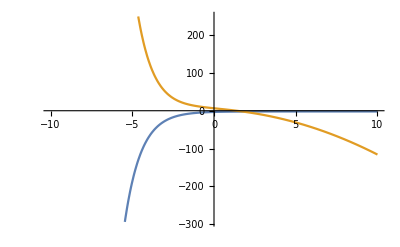

```mathematica
Plot[Evaluate[particularsol],{t,-10,10}]
```

### PROBLEM 2: x’[t]+y’[t]-2*x[t]-4*y[t]=Exp[t] x’[t]+y’[t]-y[t]=Exp[4*t] SOL:

```mathematica
sol1=DSolve[{x'[t]+y'[t]-2*x[t]-4*y[t]==Exp[t],x'[t]+y'[t]-y[t]==Exp[4*t]},{x,y},t]
```

{{x→Function[{t},-ⅇ^t (-1+ⅇ^(3 t))+1/3 (3 ⅇ^t (-1+ⅇ^(3 t))+ⅇ^(-2 t) C[1])],y→Function[{t},ⅇ^t (-1+ⅇ^(3 t))-2/9 (3 ⅇ^t (-1+ⅇ^(3 t))+ⅇ^(-2 t) C[1])]}}

```mathematica
particularsol={x[t],y[t]}/.sol1[[1]]/.{C[1]->2}
```

{-ⅇ^t (-1+ⅇ^(3 t))+1/3 (2 ⅇ^(-2 t)+3 ⅇ^t (-1+ⅇ^(3 t))),ⅇ^t (-1+ⅇ^(3 t))-2/9 (2 ⅇ^(-2 t)+3 ⅇ^t (-1+ⅇ^(3 t)))}

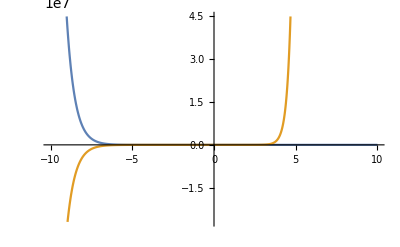

```mathematica
Plot[Evaluate[particularsol],{t,-10,10}]
```

### PROBLEM 3: x’[t]+y’[t]+4*y[t]=Sin[t] x’[t]+y’[t]-x[t]-y[t]=0 SOL:

```mathematica
sol1=DSolve[{x'[t]+y'[t]+4*y[t]==Sin[t],x'[t]+y'[t]-x[t]-y[t]==0},{x,y},t]
```

{{x→Function[{t},5/4 ⅇ^t C[1]-Sin[t]/4],y→Function[{t},-1/4 ⅇ^t C[1]+Sin[t]/4]}}

```mathematica
particularsol={x[t],y[t]}/.sol1[[1]]/.{C[1]->-1}
```

{-(5 ⅇ^t)/4-Sin[t]/4,ⅇ^t/4+Sin[t]/4}

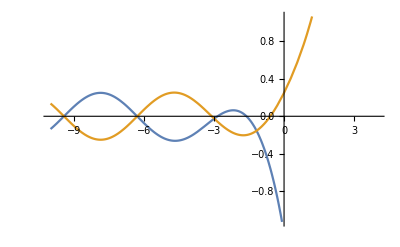

```mathematica
Plot[Evaluate[particularsol],{t,-10,4}]
```

### PROBLEM 4: 2*x’[t]+4*y’[t]+x[t]-y[t]=3Exp[t] x’[t]+y’[t]+2*x[t]+2*y[t]=Exp[t] SOL:

```mathematica
sol1=DSolve[{2*x'[t]+4*y'[t]+x[t]-y[t]==3*Exp[t],x'[t]+y'[t]+2*x[t]+2*y[t]==Exp[t]},{x,y},t]
```

{{x→Function[{t},-1/2 ⅇ^(-2 t) (-3+ⅇ^(3 t)) (ⅇ^(3 t)/2-t)-3/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) (-ⅇ^(3 t)/6+t)-1/2 ⅇ^(-2 t) (-3+ⅇ^(3 t)) C[1]-3/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) C[2]],y→Function[{t},1/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) (ⅇ^(3 t)/2-t)+1/2 ⅇ^(-2 t) (-1+3 ⅇ^(3 t)) (-ⅇ^(3 t)/6+t)+1/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) C[1]+1/2 ⅇ^(-2 t) (-1+3 ⅇ^(3 t)) C[2]]}}

```mathematica
particularsol={x[t],y[t]}/.sol1[[1]]/.{C[1]->-1,C[2]->2}
```

{1/2 ⅇ^(-2 t) (-3+ⅇ^(3 t))-3 ⅇ^(-2 t) (-1+ⅇ^(3 t))-1/2 ⅇ^(-2 t) (-3+ⅇ^(3 t)) (ⅇ^(3 t)/2-t)-3/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) (-ⅇ^(3 t)/6+t),-1/2 ⅇ^(-2 t) (-1+ⅇ^(3 t))+ⅇ^(-2 t) (-1+3 ⅇ^(3 t))+1/2 ⅇ^(-2 t) (-1+ⅇ^(3 t)) (ⅇ^(3 t)/2-t)+1/2 ⅇ^(-2 t) (-1+3 ⅇ^(3 t)) (-ⅇ^(3 t)/6+t)}

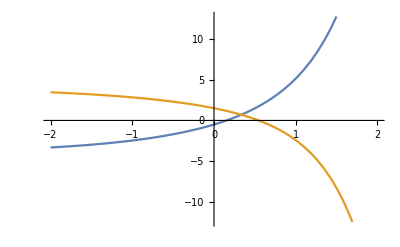

```mathematica
Plot[Evaluate[particularsol],{t,-2,2}]
```

### PROBLEM 5: x’’[t]+y’[t]=Exp[2*t] x’[t]+y’[t]-x[t]-y[t]=0 SOL:

```mathematica
sol1=DSolve[{x''[t]+y'[t]==Exp[2*t],x'[t]+y'[t]-x[t]-y[t]==0},{x,y},t]
```

{{x→Function[{t},ⅇ^t (-1+ⅇ^t)+1/2 ⅇ^(2 t) (-2+ⅇ^t) (-1+t)+1/2 ⅇ^t (-2+ⅇ^t) (-1+ⅇ^t-ⅇ^t t)-ⅇ^t (-1+t) C[1]+(-1+ⅇ^t) C[2]+(-1+ⅇ^t-ⅇ^t t) C[3]],y→Function[{t},ⅇ^t (1-ⅇ^t)-1/2 ⅇ^(2 t) (-2+ⅇ^t) t+1/2 ⅇ^t (-2+ⅇ^t) (1+ⅇ^t t)+ⅇ^t t C[1]+(1-ⅇ^t) C[2]+(1+ⅇ^t t) C[3]]}}

```mathematica
particularsol={x[t],y[t]}/.sol1[[1]]/.{C[1]->-1,C[2]->2,C[3]->2}
```

{2 (-1+ⅇ^t)+ⅇ^t (-1+ⅇ^t)+ⅇ^t (-1+t)+1/2 ⅇ^(2 t) (-2+ⅇ^t) (-1+t)+2 (-1+ⅇ^t-ⅇ^t t)+1/2 ⅇ^t (-2+ⅇ^t) (-1+ⅇ^t-ⅇ^t t),2 (1-ⅇ^t)+ⅇ^t (1-ⅇ^t)-ⅇ^t t-1/2 ⅇ^(2 t) (-2+ⅇ^t) t+2 (1+ⅇ^t t)+1/2 ⅇ^t (-2+ⅇ^t) (1+ⅇ^t t)}

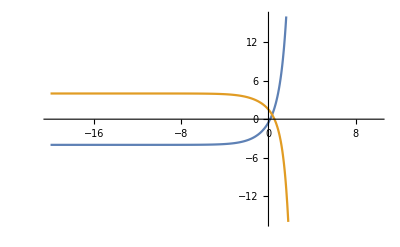

```mathematica
Plot[Evaluate[particularsol],{t,-20,10}]
```